```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

### cluster data, vary E20

```mathematica
thisData=Import["data_mechanism1//stabilityPlot_mechanism1_varyE20_8.23.23.mx"];
```

Part::partw: Part 1 of {} does not exist.

```mathematica
thisParamSet=Import["data_mechanism1//stabilityPlot_mechanism1_varyE20_8.23.23_params.mx"];
```

```mathematica
ss1={};
ss3={};
```

```mathematica
For[i=1,i<=Length[thisData],i++,

For[j=1,j<=Length[thisData[[i]]],j++,

thisCoord={thisData[[i,j,1]],thisData[[i,j,2]]};
(*check that there's an actual solution*)
If[Length[thisData[i,j,3,1]]>1,
If[Length[thisData[[i,j,3]]]==1,AppendTo[ss1,thisCoord],AppendTo[ss3,thisCoord]];
];
]
]
```

```mathematica
(*Export["stabilityPhaseDiagram_mechanism1_varyE20.png",%,ImageResolution->200]*)
```

```mathematica
ss1Height=Table[{ss1[[i,1]],ss1[[i,2]],-10},{i,Length[ss1]}];
```

```mathematica
ss3Height=Table[{ss3[[i,1]],ss3[[i,2]],10},{i,Length[ss3]}];
```

```mathematica
allPoints=Join[ss1Height,ss3Height];
```

```mathematica
(*convert allPoints to matrix format*)
```

```mathematica
xList=DeleteDuplicates[allPoints[[;;,1]]];
yList=DeleteDuplicates[allPoints[[;;,2]]]//Reverse;
```

```mathematica
plottingMatrix=ConstantArray[0,{Length[yList],Length[xList]}];
```

```mathematica
For[i=1,i<=Length[allPoints],i++,

thisPoint=allPoints[[i]];

rowIndex=Position[yList,thisPoint[[2]]][[1,1]];
colIndex=Position[xList,thisPoint[[1]]][[1,1]];

plottingMatrix[[rowIndex,colIndex]]=thisPoint[[3]];
]
```

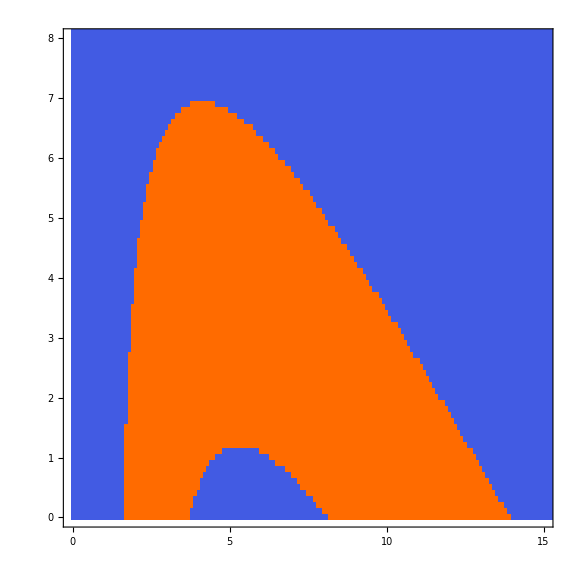

```mathematica
MatrixPlot[plottingMatrix,AspectRatio->1,Frame->{True,True,False,False},LabelStyle->Directive[Black,30],DataRange->{{xList[[1]],xList[[-1]]},{yList[[-1]],yList[[1]]}},PlotRange->{{0,15},{0,8}},ImageSize->Large]
```

```mathematica
(*Export["interference_mechanism1_phaseDiagram.png",%,ImageResolution->200]*)
```

interference_mechanism1_phaseDiagram.png

```mathematica
(*plot legend*)
```

```mathematica
legendColors={RGBColor["#475ADC"],RGBColor["#ED742E"]}
```

{RGBColor[0.2784313725490196, 0.35294117647058826, 0.8627450980392157],RGBColor[0.9294117647058824, 0.4549019607843137, 0.1803921568627451]}

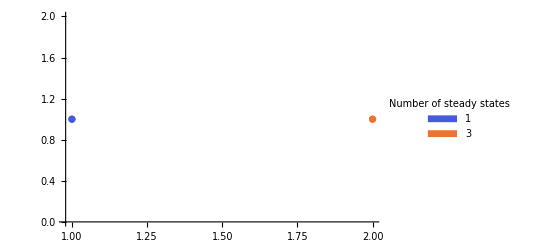

```mathematica
ListPlot[{{{1,1}},{{2,1}}},PlotLegends->SwatchLegend[{"1","3"},LegendLabel->"  Number of \nsteady states"],PlotStyle->legendColors,LabelStyle->Directive[Black, 15]]
```

```mathematica
(*Export["interference_mechanism1_phaseDiagram_legend.png",%,ImageResolution->200]*)
```

interference_mechanism1_phaseDiagram_legend.png